```mathematica
ClearAll[]

fact = 178.9818;
time=0.1;
dim=8;

Γ=Import["C:\\Users\\aless\\OneDrive - Università degli Studi di Parma\\Documents\\Lavoro\\QEC_FT\\optimization_codewords\\Gamma_08apr.txt","Table"]*fact;
γ=Array[0,{dim,dim}];
Do[γ[[m,n]]=2*Γ[[m,n]]-Γ[[m,m]]-Γ[[n,n]],{m,dim},{n,dim}];
χ=Exp[γ*time];
{eigs,vecs}=Eigensystem[χ];
(* vecs[[1]]=-vecs[[1]];
vecs[[4]]=-vecs[[4]];*)

Pr=ConstantArray[0,{dim,dim}];
Do[Pr[[k,k]]=1,{k,dim}];

(* Error operators *)
Er =ConstantArray[0,{dim,dim}];
Do[Do[Er[[j,k]]=Er[[j,k]]+Sqrt[eigs[[k]]]*vecs[[k,m]]*Pr[[j,m]],{j,dim},{m,dim}],{k,dim}]
```

```mathematica
(*Er[[All,2]]=-Er[[All,2]];*)
MatrixForm[Er]
```

(-0.922535 | 0.381173 | -0.0602274 | -0.00285216 | -0.000286784 | 0.000042507 | 3.90183×10^-6 | 0.+4.55764×10^-7 ⅈ
-0.922563 | -0.381123 | -0.0601222 | 0.00283484 | -0.00028383 | -0.0000411634 | 3.96687×10^-6 | 0.+1.54391×10^-6 ⅈ
-0.996604 | 0.0630413 | 0.0528274 | 0.00384093 | -0.000143088 | 0.0000131933 | -0.0000186942 | 0.+3.28735×10^-6 ⅈ
-0.996623 | -0.0627086 | 0.0528681 | -0.00382977 | -0.000145111 | -0.0000182718 | -1.79706×10^-6 | 0.-8.32233×10^-6 ⅈ
-0.931632 | 0.360367 | -0.0468736 | 0.000430261 | 0.000318674 | -0.0000517976 | -5.19466×10^-6 | 0.-5.80686×10^-7 ⅈ
-0.931543 | -0.360589 | -0.0469438 | -0.00040696 | 0.000314185 | 0.000049851 | -5.0864×10^-6 | 0.-2.02417×10^-6 ⅈ
-0.992866 | 0.109451 | 0.0468873 | 0.00630592 | 0.000110723 | 0.0000155021 | 0.0000166118 | 0.-9.88723×10^-7 ⅈ
-0.992845 | -0.109647 | 0.0468726 | -0.00632307 | 0.000114969 | -9.82053×10^-6 | 6.29185×10^-6 | 0.+6.62891×10^-6 ⅈ)

```mathematica
acc=0;
Do[acc=acc+Er[[k,j]]*Er[[k,j]],{k,dim},{j,dim/2}]
1-acc/dim
```

5.50267×10^-8

```mathematica
b=ConstantArray[0,{dim}];
Do[b[[k]]=1,{k,dim-1,dim}];
B=ConstantArray[0,{dim,dim}];
A=ConstantArray[0,{38,dim}];
z=ConstantArray[0,dim];
zL=ConstantArray[0,{dim}];
oL=ConstantArray[0,{dim}];
ew0=ConstantArray[0,{dim/2,dim}];
ew1=ConstantArray[0,{dim/2,dim}];
inds=Range[6];
```

```mathematica
(* code words*)
x =1;
While[x>1/1000000,
zero=Sort[Join[RandomSample[{1,3,5,7},2],RandomSample[{2,6,4,8},2]]];
(*zero ={2,4,5,7,9,12};*)
uno=Complement[Range[dim],zero];
cw=Flatten[{zero, uno}];
Do[z[[k]]=1,{k,dim/2+1,dim}];

Do[m=1; Do[Do[A[[m,j]]=Sqrt[eigs[[k]]*eigs[[l]]]*vecs[[l,cw[[j]]]]*vecs[[k,cw[[j]]]]*(-1)^z[[j]];m=m+1,{l,k,dim/2}],{k,1,dim/2}],{j,1,dim}];

Do[B[[j,k]]=A[[inds[[j]],k]],{j,1,dim-2},{k,1,dim}];
Do[B[[dim-1,k]]=z[[k]],{k,1,dim}];
Do[B[[dim,k]]=1-z[[k]],{k,1,dim}];
x=Total[Abs[Im[Sqrt[PseudoInverse[B,Tolerance->10^(-15)].b]]]]]
y=Sqrt[PseudoInverse[B,Tolerance->10^(-15)].b] ;(* we can specify Tolerance --> 0 *)
Det[B]
```

-4.44546×10^-18

```mathematica
MatrixForm[y]
```

(0.165306
0.758262
0.242771
0.582044
0.207745
0.735662
0.196197
0.614125)

```mathematica
Max[Abs[PseudoInverse[B].B-IdentityMatrix[dim]]]
```

6.14818×10^-10

```mathematica
(* determine orthogonal set of error words *)
```

```mathematica
Do[zL[[zero[[k]]]]=Re[y[[k]]],{k,1,dim/2}];
Do[oL[[uno[[k]]]]=Re[y[[k+dim/2]]],{k,1,dim/2}];
Do[ew0[[j,k]]=Er[[k,j]]*zL[[k]],{k,1,dim},{j,1,dim/2}];
Do[ew1[[j,k]]=Er[[k,j]]*oL[[k]],{k,1,dim},{j,1,dim/2}];
Subscript[ψ, 0]=Transpose[Orthogonalize[ew0]]; (* we can specify other method than Gram Schmidt and tolerance *)
Subscript[ψ, 1]=Transpose[Orthogonalize[ew1]];  (* columns are orthogonal error words *)

(* Projectors & Correctors *)
Pp=ConstantArray[0,{dim,dim,dim/2}];
Cr=ConstantArray[0,{dim,dim,dim/2}];
Do[Pp[[j,k,l]]=Subscript[ψ, 0][[j,l]]*Conjugate[Subscript[ψ, 0][[k,l]]]+Subscript[ψ, 1][[j,l]]*Conjugate[Subscript[ψ, 1][[k,l]]],{j,1,dim},{k,1,dim},{l,1,dim/2}];

Do[Subscript[θ, 0]=-ArcCos[Conjugate[zL].Subscript[ψ, 0][[All,k]]]; 
Subscript[θ, 1]=-ArcCos[Conjugate[oL].Subscript[ψ, 1][[All,k]]]; 
Subscript[v, 0]=Normalize[Subscript[ψ, 0][[All,k]]-(Conjugate[zL].Subscript[ψ, 0][[All,k]])*zL];
Subscript[v, 1]=Normalize[Subscript[ψ, 1][[All,k]]-(Conjugate[oL].Subscript[ψ, 1][[All,k]])*oL];
Cr[[All,All,k]]=Cos[Subscript[θ, 0]]*(Outer[Times,zL,Conjugate[zL]]+Outer[Times,Subscript[v, 0],Conjugate[Subscript[v, 0]]])+Sin[Subscript[θ, 0]]*(-Outer[Times,zL,Conjugate[Subscript[v, 0]]]+ Outer[Times,Subscript[v, 0],Conjugate[zL]])+Cos[Subscript[θ, 1]]*(Outer[Times,oL,Conjugate[oL]]+Outer[Times,Subscript[v, 1],Conjugate[Subscript[v, 1]]])+Sin[Subscript[θ, 1]]*(-Outer[Times,oL,Conjugate[Subscript[v, 1]]]+ Outer[Times,Subscript[v, 1],Conjugate[oL]]),{k,1,dim/2}];
```

```mathematica
(* test ideal QEC *)
α=1/Sqrt[2];
β=1/Sqrt[2];
Subscript[ψ, i]=α*zL+β*oL;
ρi=Outer[Times,Subscript[ψ, i],Subscript[ψ, i]];  (* initial state *)
ρ0=ρi;
logspace[a_,b_,n_]:=10^Range[a,b,(b-a)/(n-1)];

times=logspace[-3,0,30];
fid=ConstantArray[0,Length[times]];

Do[Do[ρ0[[j,k]]=Exp[γ[[j,k]]*times[[l]]]*ρi[[j,k]] ,{j,1,dim},{k,1,dim}];
Do[ρ=Cr[[All,All,t]].Pp[[All,All,t]].ρ0.ConjugateTranspose[Pp[[All,All,t]]].ConjugateTranspose[Cr[[All,All,t]]];fid[[l]]=fid[[l]]+Conjugate[Subscript[ψ, i]].ρ.Subscript[ψ, i],{t,1,dim/2}],{l,1,Length[times]}];
```

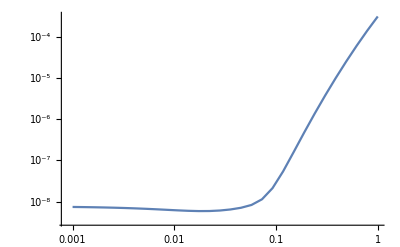

```mathematica
data=Transpose@{times,1-fid};
ListLogLogPlot[data,Joined->True]
```

```mathematica
Re[Log10[1-fid[[1]]]]
```

-8.12838

```mathematica
zero
```

{1,4,6,7}